{{x→-0.818094},{x→0.},{x→0.506308}}

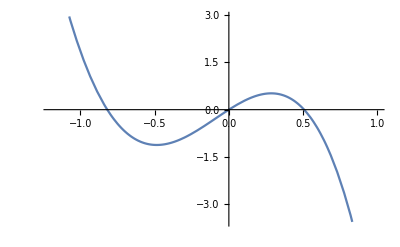

```mathematica
s1=FindRoot[1+5x-6x^3-E^(2x),{{x,-1}}];
s2=FindRoot[1+5x-6x^3-E^(2x),{{x,0}}];
s3=FindRoot[1+5x-6x^3-E^(2x),{{x,1}}];
s={s1,s2,s3}
Plot[1+5x-6x^3-E^(2x)==0,{x,-1.2,1}]
```

1/5 (1-ⅇ^(2 x)+10 x-6 x^3)

{-0.487287,1.6,-0.0239709}

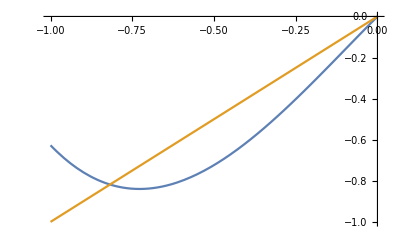

```mathematica
g1[x_]=(1+10x-6x^3-E^(2x))/5
g1'[x/.s]
Plot[{g1[x],x},{x,-1,0}]
```

(-1+ⅇ^(2 x))/(5-6 x^2)

{8.55477,0.4,2.47891}

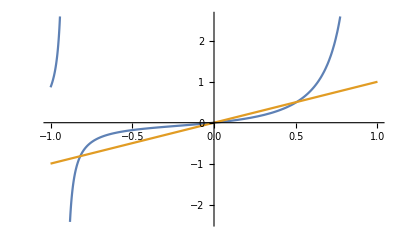

```mathematica
g2[x_]=(E^(2x)-1)/(5-6x^2)
g2'[x/.s]
Plot[{g2[x],x},{x,-1,1}]
```

1/2 Log[1+5 x-6 x^3]

{-18.0951,2.5,0.0700624}

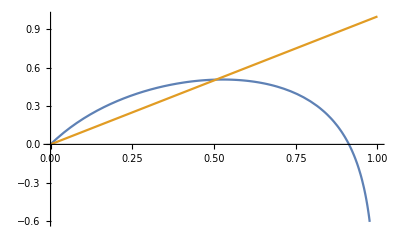

```mathematica
g3[x_]=Log[1+5x-6x^3]/2
g3'[x/.s]
Plot[{g3[x],x},{x,0,1}]
```